# Bistable networks: kinase with four states

## Finding the condition of multistationarity

Four different states for the Kinase

K1 + S -1> K1S -2> K1 + Sp     
K2 + S -3> K2S -4> K2 + Sp 
K1 -5> K2
K2S -6> K1S
K3 + S -7> K3S -8> K3 + Sp       
K2 -9> K3
K3S -10> K2S 
K4 + S -11> K4S -12> K4 + Sp     
K3 -13> K4
K4S -14> K3S
                                   
Sp-15>S  

Species
{S(1), Sp(2), K1 (3) ,K1S (4), K2(5), K2S(6), K3(7), K3S(8), K4(9), K4S(10) }

```mathematica
ClearAll["Global`*"];
A=Table[0,{15},{10}];
A[[1]][[1]]=-1;A[[1]][[3]]=-1;A[[1]][[4]]=1;
A[[2]][[2]]=1;A[[2]][[3]]=1;A[[2]][[4]]=-1;
A[[3]][[1]]=-1;A[[3]][[5]]=-1;A[[3]][[6]]=1;
A[[4]][[2]]=1;A[[4]][[5]]=1;A[[4]][[6]]=-1;
A[[5]][[3]]=-1;A[[5]][[5]]=1;
A[[6]][[4]]=1;A[[6]][[6]]=-1;
A[[7]][[1]]=-1;A[[7]][[7]]=-1;A[[7]][[8]]=1;
A[[8]][[8]]=-1;A[[8]][[7]]=1;A[[8]][[2]]=1;
A[[9]][[5]]=-1;A[[9]][[7]]=1;
A[[10]][[8]]=-1;A[[10]][[6]]=1;
A[[11]][[1]]=-1;A[[11]][[9]]=-1;A[[11]][[10]]=1;
A[[12]][[10]]=-1;A[[12]][[9]]=1;A[[12]][[2]]=1;
A[[13]][[7]]=-1;A[[13]][[9]]=1;
A[[14]][[10]]=-1;A[[14]][[8]]=1;
A[[15]][[2]]=-1;A[[15]][[1]]=1;
stoiM=Transpose[A]
```

{{-1,0,-1,0,0,0,-1,0,0,0,-1,0,0,0,1},{0,1,0,1,0,0,0,1,0,0,0,1,0,0,-1},{-1,1,0,0,-1,0,0,0,0,0,0,0,0,0,0},{1,-1,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,-1,1,1,0,0,0,-1,0,0,0,0,0,0},{0,0,1,-1,0,-1,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,-1,1,1,0,0,0,-1,0,0},{0,0,0,0,0,0,1,-1,0,-1,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,-1,1,1,0,0},{0,0,0,0,0,0,0,0,0,0,1,-1,0,-1,0}}

```mathematica
ks={Subscript[k, 1]*Subscript[x, 1]*Subscript[x, 3],Subscript[k, 2]*Subscript[x, 4],Subscript[k, 3]*Subscript[x, 1]*Subscript[x, 5],Subscript[k, 4]*Subscript[x, 6],Subscript[k, 5]*Subscript[x, 3],Subscript[k, 6]*Subscript[x, 6],Subscript[k, 7]*Subscript[x, 1]*Subscript[x, 7],Subscript[k, 8]*Subscript[x, 8],Subscript[k, 9]*Subscript[x, 5],Subscript[k, 10]*Subscript[x, 8],Subscript[k, 11]*Subscript[x, 1]*Subscript[x, 9],Subscript[k, 12]*Subscript[x, 10],Subscript[k, 13]*Subscript[x, 7],Subscript[k, 14]*Subscript[x, 10],Subscript[k, 15]*Subscript[x, 2]}
```

{k_1 x_1 x_3,k_2 x_4,k_3 x_1 x_5,k_4 x_6,k_5 x_3,k_6 x_6,k_7 x_1 x_7,k_8 x_8,k_9 x_5,k_10 x_8,k_11 x_1 x_9,k_12 x_10,k_13 x_7,k_14 x_10,k_15 x_2}

```mathematica
ssEqns=stoiM.ks
```

{k_15 x_2-k_1 x_1 x_3-k_3 x_1 x_5-k_7 x_1 x_7-k_11 x_1 x_9,-k_15 x_2+k_2 x_4+k_4 x_6+k_8 x_8+k_12 x_10,-k_5 x_3-k_1 x_1 x_3+k_2 x_4,k_1 x_1 x_3-k_2 x_4+k_6 x_6,k_5 x_3-k_9 x_5-k_3 x_1 x_5+k_4 x_6,k_3 x_1 x_5-k_4 x_6-k_6 x_6+k_10 x_8,k_9 x_5-k_13 x_7-k_7 x_1 x_7+k_8 x_8,k_7 x_1 x_7-k_8 x_8-k_10 x_8+k_14 x_10,k_13 x_7-k_11 x_1 x_9+k_12 x_10,k_11 x_1 x_9-k_12 x_10-k_14 x_10}

```mathematica
mC=RowReduce[NullSpace[A]]
```

{{1,1,0,1,0,1,0,1,0,1},{0,0,1,1,1,1,1,1,1,1}}

```mathematica
cons={Subscript[x, 1]+Subscript[x, 2]+Subscript[x, 4]+Subscript[x, 6]+Subscript[x, 8]+Subscript[x, 10]-Subscript[T, 1],Subscript[x, 3]+Subscript[x, 4]+Subscript[x, 5]+Subscript[x, 6]+Subscript[x, 7]+Subscript[x, 8]+Subscript[x, 9]+Subscript[x, 10]-Subscript[T, 2]}
```

{-T_1+x_1+x_2+x_4+x_6+x_8+x_10,-T_2+x_3+x_4+x_5+x_6+x_7+x_8+x_9+x_10}

```mathematica
sol1=Solve[Flatten[{cons[[2]],ssEqns[[2;;10]]}]==0,{Subscript[x, 2],Subscript[x, 3],Subscript[x, 4],Subscript[x, 5],Subscript[x, 6],Subscript[x, 7],Subscript[x, 8],Subscript[x, 9],Subscript[x, 10]}]
```

{{x_2→-((k_2^2 k_5 (k_2 k_4 k_5+k_2 k_5 k_6) k_10 k_11^2 k_14 T_2 x_1^2 (-k_13-k_7 x_1) ((-k_9 k_10 k_12 k_13+k_3 k_8 k_12 k_13 x_1+k_3 k_8 k_13 k_14 x_1+k_3 k_7 k_8 k_14 x_1^2)/(k_10 k_14 k_15 (k_13+k_7 x_1))-((-k_9-k_3 x_1) ((-k_4 k_5-k_5 k_6-k_1 k_6 x_1)/(k_5 k_15)-((-k_4-k_6) (-k_8/k_15-(k_8 k_12 k_13)/(k_14 k_15 (k_13+k_7 x_1))))/k_10))/(k_4+k_6)))/(-k_2 k_5 (-k_9-k_3 x_1) (k_10 k_11 k_14 x_1 (-k_13-k_7 x_1) (k_2 k_5 (k_2 k_11 x_1+k_6 k_11 x_1)+k_2 k_6 (k_2 k_11 x_1+k_1 k_11 x_1^2))-(-k_4-k_6) (k_2^2 k_5 k_11^2 k_14 x_1^2 (-k_13-k_7 x_1)-k_8 (k_2 k_5 k_11 k_13 x_1 (k_2 k_12+k_2 k_11 x_1)+k_2 k_5 k_11 k_14 x_1 (k_2 k_13+k_2 k_11 x_1))))+(k_2 k_4 k_5+k_2 k_5 k_6) (-k_3 x_1 (k_2^2 k_5 k_11^2 k_14 x_1^2 (-k_13-k_7 x_1)-k_8 (k_2 k_5 k_11 k_13 x_1 (k_2 k_12+k_2 k_11 x_1)+k_2 k_5 k_11 k_14 x_1 (k_2 k_13+k_2 k_11 x_1)))+k_10 (k_2^2 k_5 k_11^2 k_14 x_1^2 (-k_13-k_7 x_1)-k_9 (k_2 k_5 k_11 k_13 x_1 (k_2 k_12+k_2 k_11 x_1)+k_2 k_5 k_11 k_14 x_1 (k_2 k_13+k_2 k_11 x_1)))))),x_3→(k_2^2 k_6 (k_2 k_4 k_5+k_2 k_5 k_6) k_10 k_11^2 k_14 T_2 x_1^2 (k_9+k_3 x_1) (-k_13-k_7 x_1))/((k_4+k_6) (-k_2 k_5 (-k_9-k_3 x_1) (k_10 k_11 k_14 x_1 (-k_13-k_7 x_1) (k_2 k_5 (k_2 k_11 x_1+k_6 k_11 x_1)+k_2 k_6 (k_2 k_11 x_1+k_1 k_11 x_1^2))-(-k_4-k_6) (k_2^2 k_5 k_11^2 k_14 x_1^2 (-k_13-k_7 x_1)-k_8 (k_2 k_5 k_11 k_13 x_1 (k_2 k_12+k_2 k_11 x_1)+k_2 k_5 k_11 k_14 x_1 (k_2 k_13+k_2 k_11 x_1))))+(k_2 k_4 k_5+k_2 k_5 k_6) (-k_3 x_1 (k_2^2 k_5 k_11^2 k_14 x_1^2 (-k_13-k_7 x_1)-k_8 (k_2 k_5 k_11 k_13 x_1 (k_2 k_12+k_2 k_11 x_1)+k_2 k_5 k_11 k_14 x_1 (k_2 k_13+k_2 k_11 x_1)))+k_10 (k_2^2 k_5 k_11^2 k_14 x_1^2 (-k_13-k_7 x_1)-k_9 (k_2 k_5 k_11 k_13 x_1 (k_2 k_12+k_2 k_11 x_1)+k_2 k_5 k_11 k_14 x_1 (k_2 k_13+k_2 k_11 x_1)))))),x_4→(k_2 k_6 (k_2 k_4 k_5+k_2 k_5 k_6) k_10 k_11^2 k_14 T_2 x_1^2 (k_5+k_1 x_1) (k_9+k_3 x_1) (-k_13-k_7 x_1))/((k_4+k_6) (-k_2 k_5 (-k_9-k_3 x_1) (k_10 k_11 k_14 x_1 (-k_13-k_7 x_1) (k_2 k_5 (k_2 k_11 x_1+k_6 k_11 x_1)+k_2 k_6 (k_2 k_11 x_1+k_1 k_11 x_1^2))-(-k_4-k_6) (k_2^2 k_5 k_11^2 k_14 x_1^2 (-k_13-k_7 x_1)-k_8 (k_2 k_5 k_11 k_13 x_1 (k_2 k_12+k_2 k_11 x_1)+k_2 k_5 k_11 k_14 x_1 (k_2 k_13+k_2 k_11 x_1))))+(k_2 k_4 k_5+k_2 k_5 k_6) (-k_3 x_1 (k_2^2 k_5 k_11^2 k_14 x_1^2 (-k_13-k_7 x_1)-k_8 (k_2 k_5 k_11 k_13 x_1 (k_2 k_12+k_2 k_11 x_1)+k_2 k_5 k_11 k_14 x_1 (k_2 k_13+k_2 k_11 x_1)))+k_10 (k_2^2 k_5 k_11^2 k_14 x_1^2 (-k_13-k_7 x_1)-k_9 (k_2 k_5 k_11 k_13 x_1 (k_2 k_12+k_2 k_11 x_1)+k_2 k_5 k_11 k_14 x_1 (k_2 k_13+k_2 k_11 x_1)))))),x_5→(k_2^2 k_5 (k_2 k_4 k_5+k_2 k_5 k_6) k_10 k_11^2 k_14 T_2 x_1^2 (-k_13-k_7 x_1))/(-k_2 k_5 (-k_9-k_3 x_1) (k_10 k_11 k_14 x_1 (-k_13-k_7 x_1) (k_2 k_5 (k_2 k_11 x_1+k_6 k_11 x_1)+k_2 k_6 (k_2 k_11 x_1+k_1 k_11 x_1^2))-(-k_4-k_6) (k_2^2 k_5 k_11^2 k_14 x_1^2 (-k_13-k_7 x_1)-k_8 (k_2 k_5 k_11 k_13 x_1 (k_2 k_12+k_2 k_11 x_1)+k_2 k_5 k_11 k_14 x_1 (k_2 k_13+k_2 k_11 x_1))))+(k_2 k_4 k_5+k_2 k_5 k_6) (-k_3 x_1 (k_2^2 k_5 k_11^2 k_14 x_1^2 (-k_13-k_7 x_1)-k_8 (k_2 k_5 k_11 k_13 x_1 (k_2 k_12+k_2 k_11 x_1)+k_2 k_5 k_11 k_14 x_1 (k_2 k_13+k_2 k_11 x_1)))+k_10 (k_2^2 k_5 k_11^2 k_14 x_1^2 (-k_13-k_7 x_1)-k_9 (k_2 k_5 k_11 k_13 x_1 (k_2 k_12+k_2 k_11 x_1)+k_2 k_5 k_11 k_14 x_1 (k_2 k_13+k_2 k_11 x_1))))),x_6→-((k_2^2 k_5 (k_2 k_4 k_5+k_2 k_5 k_6) k_10 k_11^2 k_14 T_2 x_1^2 (-k_9-k_3 x_1) (-k_13-k_7 x_1))/((k_4+k_6) (-k_2 k_5 (-k_9-k_3 x_1) (k_10 k_11 k_14 x_1 (-k_13-k_7 x_1) (k_2 k_5 (k_2 k_11 x_1+k_6 k_11 x_1)+k_2 k_6 (k_2 k_11 x_1+k_1 k_11 x_1^2))-(-k_4-k_6) (k_2^2 k_5 k_11^2 k_14 x_1^2 (-k_13-k_7 x_1)-k_8 (k_2 k_5 k_11 k_13 x_1 (k_2 k_12+k_2 k_11 x_1)+k_2 k_5 k_11 k_14 x_1 (k_2 k_13+k_2 k_11 x_1))))+(k_2 k_4 k_5+k_2 k_5 k_6) (-k_3 x_1 (k_2^2 k_5 k_11^2 k_14 x_1^2 (-k_13-k_7 x_1)-k_8 (k_2 k_5 k_11 k_13 x_1 (k_2 k_12+k_2 k_11 x_1)+k_2 k_5 k_11 k_14 x_1 (k_2 k_13+k_2 k_11 x_1)))+k_10 (k_2^2 k_5 k_11^2 k_14 x_1^2 (-k_13-k_7 x_1)-k_9 (k_2 k_5 k_11 k_13 x_1 (k_2 k_12+k_2 k_11 x_1)+k_2 k_5 k_11 k_14 x_1 (k_2 k_13+k_2 k_11 x_1))))))),x_7→(k_2^2 k_5 (k_2 k_4 k_5+k_2 k_5 k_6) k_9 (k_8+k_10) k_11^2 k_14 T_2 x_1^2 (-k_13-k_7 x_1))/((k_13+k_7 x_1) (-k_2 k_5 (-k_9-k_3 x_1) (k_10 k_11 k_14 x_1 (-k_13-k_7 x_1) (k_2 k_5 (k_2 k_11 x_1+k_6 k_11 x_1)+k_2 k_6 (k_2 k_11 x_1+k_1 k_11 x_1^2))-(-k_4-k_6) (k_2^2 k_5 k_11^2 k_14 x_1^2 (-k_13-k_7 x_1)-k_8 (k_2 k_5 k_11 k_13 x_1 (k_2 k_12+k_2 k_11 x_1)+k_2 k_5 k_11 k_14 x_1 (k_2 k_13+k_2 k_11 x_1))))+(k_2 k_4 k_5+k_2 k_5 k_6) (-k_3 x_1 (k_2^2 k_5 k_11^2 k_14 x_1^2 (-k_13-k_7 x_1)-k_8 (k_2 k_5 k_11 k_13 x_1 (k_2 k_12+k_2 k_11 x_1)+k_2 k_5 k_11 k_14 x_1 (k_2 k_13+k_2 k_11 x_1)))+k_10 (k_2^2 k_5 k_11^2 k_14 x_1^2 (-k_13-k_7 x_1)-k_9 (k_2 k_5 k_11 k_13 x_1 (k_2 k_12+k_2 k_11 x_1)+k_2 k_5 k_11 k_14 x_1 (k_2 k_13+k_2 k_11 x_1)))))),x_8→(k_2^2 k_5 (k_2 k_4 k_5+k_2 k_5 k_6) k_9 k_11^2 k_14 T_2 x_1^2 (-k_13-k_7 x_1))/(-k_2 k_5 (-k_9-k_3 x_1) (k_10 k_11 k_14 x_1 (-k_13-k_7 x_1) (k_2 k_5 (k_2 k_11 x_1+k_6 k_11 x_1)+k_2 k_6 (k_2 k_11 x_1+k_1 k_11 x_1^2))-(-k_4-k_6) (k_2^2 k_5 k_11^2 k_14 x_1^2 (-k_13-k_7 x_1)-k_8 (k_2 k_5 k_11 k_13 x_1 (k_2 k_12+k_2 k_11 x_1)+k_2 k_5 k_11 k_14 x_1 (k_2 k_13+k_2 k_11 x_1))))+(k_2 k_4 k_5+k_2 k_5 k_6) (-k_3 x_1 (k_2^2 k_5 k_11^2 k_14 x_1^2 (-k_13-k_7 x_1)-k_8 (k_2 k_5 k_11 k_13 x_1 (k_2 k_12+k_2 k_11 x_1)+k_2 k_5 k_11 k_14 x_1 (k_2 k_13+k_2 k_11 x_1)))+k_10 (k_2^2 k_5 k_11^2 k_14 x_1^2 (-k_13-k_7 x_1)-k_9 (k_2 k_5 k_11 k_13 x_1 (k_2 k_12+k_2 k_11 x_1)+k_2 k_5 k_11 k_14 x_1 (k_2 k_13+k_2 k_11 x_1))))),x_9→-((k_2^2 k_5 (k_2 k_4 k_5+k_2 k_5 k_6) k_11 (-k_8 k_9 k_12 k_13-k_9 k_10 k_12 k_13-k_8 k_9 k_13 k_14-k_9 k_10 k_13 k_14) T_2 x_1 (-k_13-k_7 x_1))/((k_13+k_7 x_1) (-k_2 k_5 (-k_9-k_3 x_1) (k_10 k_11 k_14 x_1 (-k_13-k_7 x_1) (k_2 k_5 (k_2 k_11 x_1+k_6 k_11 x_1)+k_2 k_6 (k_2 k_11 x_1+k_1 k_11 x_1^2))-(-k_4-k_6) (k_2^2 k_5 k_11^2 k_14 x_1^2 (-k_13-k_7 x_1)-k_8 (k_2 k_5 k_11 k_13 x_1 (k_2 k_12+k_2 k_11 x_1)+k_2 k_5 k_11 k_14 x_1 (k_2 k_13+k_2 k_11 x_1))))+(k_2 k_4 k_5+k_2 k_5 k_6) (-k_3 x_1 (k_2^2 k_5 k_11^2 k_14 x_1^2 (-k_13-k_7 x_1)-k_8 (k_2 k_5 k_11 k_13 x_1 (k_2 k_12+k_2 k_11 x_1)+k_2 k_5 k_11 k_14 x_1 (k_2 k_13+k_2 k_11 x_1)))+k_10 (k_2^2 k_5 k_11^2 k_14 x_1^2 (-k_13-k_7 x_1)-k_9 (k_2 k_5 k_11 k_13 x_1 (k_2 k_12+k_2 k_11 x_1)+k_2 k_5 k_11 k_14 x_1 (k_2 k_13+k_2 k_11 x_1))))))),x_10→(k_2^2 k_5 (k_2 k_4 k_5+k_2 k_5 k_6) k_9 (k_8+k_10) k_11^2 k_13 T_2 x_1^2 (-k_13-k_7 x_1))/((k_13+k_7 x_1) (-k_2 k_5 (-k_9-k_3 x_1) (k_10 k_11 k_14 x_1 (-k_13-k_7 x_1) (k_2 k_5 (k_2 k_11 x_1+k_6 k_11 x_1)+k_2 k_6 (k_2 k_11 x_1+k_1 k_11 x_1^2))-(-k_4-k_6) (k_2^2 k_5 k_11^2 k_14 x_1^2 (-k_13-k_7 x_1)-k_8 (k_2 k_5 k_11 k_13 x_1 (k_2 k_12+k_2 k_11 x_1)+k_2 k_5 k_11 k_14 x_1 (k_2 k_13+k_2 k_11 x_1))))+(k_2 k_4 k_5+k_2 k_5 k_6) (-k_3 x_1 (k_2^2 k_5 k_11^2 k_14 x_1^2 (-k_13-k_7 x_1)-k_8 (k_2 k_5 k_11 k_13 x_1 (k_2 k_12+k_2 k_11 x_1)+k_2 k_5 k_11 k_14 x_1 (k_2 k_13+k_2 k_11 x_1)))+k_10 (k_2^2 k_5 k_11^2 k_14 x_1^2 (-k_13-k_7 x_1)-k_9 (k_2 k_5 k_11 k_13 x_1 (k_2 k_12+k_2 k_11 x_1)+k_2 k_5 k_11 k_14 x_1 (k_2 k_13+k_2 k_11 x_1))))))}}

```mathematica
term=Simplify[cons[[1]]/.sol1[[1]]]
```

(-k_6 k_10 k_11 k_14 k_15 (T_1-T_2-x_1) x_1 (k_5+k_1 x_1) (k_9+k_3 x_1) (k_13+k_7 x_1)+k_2 (k_6 k_10 k_11 k_14 x_1 (k_9+k_3 x_1) (k_13+k_7 x_1) (k_1 T_2 x_1+k_15 (-T_1+x_1))+k_4 k_5 (k_10 k_11 k_14 x_1 (k_13+k_7 x_1) (k_3 T_2 x_1+k_15 (-T_1+x_1))+k_8 k_9 (k_11 k_14 x_1 (k_7 T_2 x_1+k_15 (-T_1+x_1))+k_12 k_13 (k_11 T_2 x_1+k_15 (-T_1+x_1))+k_13 (k_11 k_15 x_1 (-T_1+T_2+x_1)+k_14 (k_11 T_2 x_1+k_15 (-T_1+x_1))))+k_9 (-k_11 k_14 k_15 (T_1-T_2-x_1) x_1 (k_13+k_7 x_1)+k_10 (k_11 k_14 x_1 (k_7 T_2 x_1+k_15 (-T_1+x_1))+k_12 k_13 (k_11 T_2 x_1+k_15 (-T_1+x_1))+k_13 (k_11 k_15 x_1 (-T_1+T_2+x_1)+k_14 (k_11 T_2 x_1+k_15 (-T_1+x_1))))))+k_5 (-k_10 k_11 k_14 k_15 (T_1-T_2-x_1) x_1 (k_9+k_3 x_1) (k_13+k_7 x_1)+k_6 (k_10 k_11 k_14 x_1 (k_13+k_7 x_1) (k_3 T_2 x_1+k_15 (-T_1+x_1))+k_8 k_9 (k_11 k_14 x_1 (k_7 T_2 x_1+k_15 (-T_1+x_1))+k_12 k_13 (k_11 T_2 x_1+k_15 (-T_1+x_1))+k_13 (k_11 k_15 x_1 (-T_1+T_2+x_1)+k_14 (k_11 T_2 x_1+k_15 (-T_1+x_1))))+k_9 (-k_11 k_14 k_15 (T_1-T_2-x_1) x_1 (k_13+k_7 x_1)+k_10 (k_11 k_14 x_1 (k_7 T_2 x_1+k_15 (-T_1+x_1))+k_12 k_13 (k_11 T_2 x_1+k_15 (-T_1+x_1))+k_13 (k_11 k_15 x_1 (-T_1+T_2+x_1)+k_14 (k_11 T_2 x_1+k_15 (-T_1+x_1)))))))))/(k_15 (k_6 k_10 k_11 k_14 x_1 (k_5+k_1 x_1) (k_9+k_3 x_1) (k_13+k_7 x_1)+k_2 (k_6 k_10 k_11 k_14 x_1 (k_9+k_3 x_1) (k_13+k_7 x_1)+k_4 k_5 (k_10 k_11 k_14 x_1 (k_13+k_7 x_1)+k_8 k_9 (k_12 k_13+k_11 k_14 x_1+k_13 (k_14+k_11 x_1))+k_9 (k_11 k_14 x_1 (k_13+k_7 x_1)+k_10 (k_12 k_13+k_11 k_14 x_1+k_13 (k_14+k_11 x_1))))+k_5 (k_10 k_11 k_14 x_1 (k_9+k_3 x_1) (k_13+k_7 x_1)+k_6 (k_10 k_11 k_14 x_1 (k_13+k_7 x_1)+k_8 k_9 (k_12 k_13+k_11 k_14 x_1+k_13 (k_14+k_11 x_1))+k_9 (k_11 k_14 x_1 (k_13+k_7 x_1)+k_10 (k_12 k_13+k_11 k_14 x_1+k_13 (k_14+k_11 x_1))))))))

```mathematica
Together[term]
```

(-k_2 k_4 k_5 k_8 k_9 k_12 k_13 k_15 T_1-k_2 k_5 k_6 k_8 k_9 k_12 k_13 k_15 T_1-k_2 k_4 k_5 k_9 k_10 k_12 k_13 k_15 T_1-k_2 k_5 k_6 k_9 k_10 k_12 k_13 k_15 T_1-k_2 k_4 k_5 k_8 k_9 k_13 k_14 k_15 T_1-k_2 k_5 k_6 k_8 k_9 k_13 k_14 k_15 T_1-k_2 k_4 k_5 k_9 k_10 k_13 k_14 k_15 T_1-k_2 k_5 k_6 k_9 k_10 k_13 k_14 k_15 T_1+k_2 k_4 k_5 k_8 k_9 k_12 k_13 k_15 x_1+k_2 k_5 k_6 k_8 k_9 k_12 k_13 k_15 x_1+k_2 k_4 k_5 k_9 k_10 k_12 k_13 k_15 x_1+k_2 k_5 k_6 k_9 k_10 k_12 k_13 k_15 x_1+k_2 k_4 k_5 k_8 k_9 k_13 k_14 k_15 x_1+k_2 k_5 k_6 k_8 k_9 k_13 k_14 k_15 x_1+k_2 k_4 k_5 k_9 k_10 k_13 k_14 k_15 x_1+k_2 k_5 k_6 k_9 k_10 k_13 k_14 k_15 x_1-k_2 k_4 k_5 k_8 k_9 k_11 k_13 k_15 T_1 x_1-k_2 k_5 k_6 k_8 k_9 k_11 k_13 k_15 T_1 x_1-k_2 k_4 k_5 k_9 k_10 k_11 k_13 k_15 T_1 x_1-k_2 k_5 k_6 k_9 k_10 k_11 k_13 k_15 T_1 x_1-k_2 k_4 k_5 k_8 k_9 k_11 k_14 k_15 T_1 x_1-k_2 k_5 k_6 k_8 k_9 k_11 k_14 k_15 T_1 x_1-k_2 k_4 k_5 k_9 k_10 k_11 k_14 k_15 T_1 x_1-k_2 k_5 k_6 k_9 k_10 k_11 k_14 k_15 T_1 x_1-k_2 k_4 k_5 k_9 k_11 k_13 k_14 k_15 T_1 x_1-k_2 k_5 k_6 k_9 k_11 k_13 k_14 k_15 T_1 x_1-k_2 k_4 k_5 k_10 k_11 k_13 k_14 k_15 T_1 x_1-k_2 k_5 k_6 k_10 k_11 k_13 k_14 k_15 T_1 x_1-k_2 k_5 k_9 k_10 k_11 k_13 k_14 k_15 T_1 x_1-k_2 k_6 k_9 k_10 k_11 k_13 k_14 k_15 T_1 x_1-k_5 k_6 k_9 k_10 k_11 k_13 k_14 k_15 T_1 x_1+k_2 k_4 k_5 k_8 k_9 k_11 k_12 k_13 T_2 x_1+k_2 k_5 k_6 k_8 k_9 k_11 k_12 k_13 T_2 x_1+k_2 k_4 k_5 k_9 k_10 k_11 k_12 k_13 T_2 x_1+k_2 k_5 k_6 k_9 k_10 k_11 k_12 k_13 T_2 x_1+k_2 k_4 k_5 k_8 k_9 k_11 k_13 k_14 T_2 x_1+k_2 k_5 k_6 k_8 k_9 k_11 k_13 k_14 T_2 x_1+k_2 k_4 k_5 k_9 k_10 k_11 k_13 k_14 T_2 x_1+k_2 k_5 k_6 k_9 k_10 k_11 k_13 k_14 T_2 x_1+k_2 k_4 k_5 k_8 k_9 k_11 k_13 k_15 T_2 x_1+k_2 k_5 k_6 k_8 k_9 k_11 k_13 k_15 T_2 x_1+k_2 k_4 k_5 k_9 k_10 k_11 k_13 k_15 T_2 x_1+k_2 k_5 k_6 k_9 k_10 k_11 k_13 k_15 T_2 x_1+k_2 k_4 k_5 k_9 k_11 k_13 k_14 k_15 T_2 x_1+k_2 k_5 k_6 k_9 k_11 k_13 k_14 k_15 T_2 x_1+k_2 k_5 k_9 k_10 k_11 k_13 k_14 k_15 T_2 x_1+k_5 k_6 k_9 k_10 k_11 k_13 k_14 k_15 T_2 x_1+k_2 k_4 k_5 k_8 k_9 k_11 k_13 k_15 x_1^2+k_2 k_5 k_6 k_8 k_9 k_11 k_13 k_15 x_1^2+k_2 k_4 k_5 k_9 k_10 k_11 k_13 k_15 x_1^2+k_2 k_5 k_6 k_9 k_10 k_11 k_13 k_15 x_1^2+k_2 k_4 k_5 k_8 k_9 k_11 k_14 k_15 x_1^2+k_2 k_5 k_6 k_8 k_9 k_11 k_14 k_15 x_1^2+k_2 k_4 k_5 k_9 k_10 k_11 k_14 k_15 x_1^2+k_2 k_5 k_6 k_9 k_10 k_11 k_14 k_15 x_1^2+k_2 k_4 k_5 k_9 k_11 k_13 k_14 k_15 x_1^2+k_2 k_5 k_6 k_9 k_11 k_13 k_14 k_15 x_1^2+k_2 k_4 k_5 k_10 k_11 k_13 k_14 k_15 x_1^2+k_2 k_5 k_6 k_10 k_11 k_13 k_14 k_15 x_1^2+k_2 k_5 k_9 k_10 k_11 k_13 k_14 k_15 x_1^2+k_2 k_6 k_9 k_10 k_11 k_13 k_14 k_15 x_1^2+k_5 k_6 k_9 k_10 k_11 k_13 k_14 k_15 x_1^2-k_2 k_4 k_5 k_7 k_9 k_11 k_14 k_15 T_1 x_1^2-k_2 k_5 k_6 k_7 k_9 k_11 k_14 k_15 T_1 x_1^2-k_2 k_4 k_5 k_7 k_10 k_11 k_14 k_15 T_1 x_1^2-k_2 k_5 k_6 k_7 k_10 k_11 k_14 k_15 T_1 x_1^2-k_2 k_5 k_7 k_9 k_10 k_11 k_14 k_15 T_1 x_1^2-k_2 k_6 k_7 k_9 k_10 k_11 k_14 k_15 T_1 x_1^2-k_5 k_6 k_7 k_9 k_10 k_11 k_14 k_15 T_1 x_1^2-k_2 k_3 k_5 k_10 k_11 k_13 k_14 k_15 T_1 x_1^2-k_2 k_3 k_6 k_10 k_11 k_13 k_14 k_15 T_1 x_1^2-k_3 k_5 k_6 k_10 k_11 k_13 k_14 k_15 T_1 x_1^2-k_1 k_6 k_9 k_10 k_11 k_13 k_14 k_15 T_1 x_1^2+k_2 k_4 k_5 k_7 k_8 k_9 k_11 k_14 T_2 x_1^2+k_2 k_5 k_6 k_7 k_8 k_9 k_11 k_14 T_2 x_1^2+k_2 k_4 k_5 k_7 k_9 k_10 k_11 k_14 T_2 x_1^2+k_2 k_5 k_6 k_7 k_9 k_10 k_11 k_14 T_2 x_1^2+k_2 k_3 k_4 k_5 k_10 k_11 k_13 k_14 T_2 x_1^2+k_2 k_3 k_5 k_6 k_10 k_11 k_13 k_14 T_2 x_1^2+k_1 k_2 k_6 k_9 k_10 k_11 k_13 k_14 T_2 x_1^2+k_2 k_4 k_5 k_7 k_9 k_11 k_14 k_15 T_2 x_1^2+k_2 k_5 k_6 k_7 k_9 k_11 k_14 k_15 T_2 x_1^2+k_2 k_5 k_7 k_9 k_10 k_11 k_14 k_15 T_2 x_1^2+k_5 k_6 k_7 k_9 k_10 k_11 k_14 k_15 T_2 x_1^2+k_2 k_3 k_5 k_10 k_11 k_13 k_14 k_15 T_2 x_1^2+k_3 k_5 k_6 k_10 k_11 k_13 k_14 k_15 T_2 x_1^2+k_1 k_6 k_9 k_10 k_11 k_13 k_14 k_15 T_2 x_1^2+k_2 k_4 k_5 k_7 k_9 k_11 k_14 k_15 x_1^3+k_2 k_5 k_6 k_7 k_9 k_11 k_14 k_15 x_1^3+k_2 k_4 k_5 k_7 k_10 k_11 k_14 k_15 x_1^3+k_2 k_5 k_6 k_7 k_10 k_11 k_14 k_15 x_1^3+k_2 k_5 k_7 k_9 k_10 k_11 k_14 k_15 x_1^3+k_2 k_6 k_7 k_9 k_10 k_11 k_14 k_15 x_1^3+k_5 k_6 k_7 k_9 k_10 k_11 k_14 k_15 x_1^3+k_2 k_3 k_5 k_10 k_11 k_13 k_14 k_15 x_1^3+k_2 k_3 k_6 k_10 k_11 k_13 k_14 k_15 x_1^3+k_3 k_5 k_6 k_10 k_11 k_13 k_14 k_15 x_1^3+k_1 k_6 k_9 k_10 k_11 k_13 k_14 k_15 x_1^3-k_2 k_3 k_5 k_7 k_10 k_11 k_14 k_15 T_1 x_1^3-k_2 k_3 k_6 k_7 k_10 k_11 k_14 k_15 T_1 x_1^3-k_3 k_5 k_6 k_7 k_10 k_11 k_14 k_15 T_1 x_1^3-k_1 k_6 k_7 k_9 k_10 k_11 k_14 k_15 T_1 x_1^3-k_1 k_3 k_6 k_10 k_11 k_13 k_14 k_15 T_1 x_1^3+k_2 k_3 k_4 k_5 k_7 k_10 k_11 k_14 T_2 x_1^3+k_2 k_3 k_5 k_6 k_7 k_10 k_11 k_14 T_2 x_1^3+k_1 k_2 k_6 k_7 k_9 k_10 k_11 k_14 T_2 x_1^3+k_1 k_2 k_3 k_6 k_10 k_11 k_13 k_14 T_2 x_1^3+k_2 k_3 k_5 k_7 k_10 k_11 k_14 k_15 T_2 x_1^3+k_3 k_5 k_6 k_7 k_10 k_11 k_14 k_15 T_2 x_1^3+k_1 k_6 k_7 k_9 k_10 k_11 k_14 k_15 T_2 x_1^3+k_1 k_3 k_6 k_10 k_11 k_13 k_14 k_15 T_2 x_1^3+k_2 k_3 k_5 k_7 k_10 k_11 k_14 k_15 x_1^4+k_2 k_3 k_6 k_7 k_10 k_11 k_14 k_15 x_1^4+k_3 k_5 k_6 k_7 k_10 k_11 k_14 k_15 x_1^4+k_1 k_6 k_7 k_9 k_10 k_11 k_14 k_15 x_1^4+k_1 k_3 k_6 k_10 k_11 k_13 k_14 k_15 x_1^4-k_1 k_3 k_6 k_7 k_10 k_11 k_14 k_15 T_1 x_1^4+k_1 k_2 k_3 k_6 k_7 k_10 k_11 k_14 T_2 x_1^4+k_1 k_3 k_6 k_7 k_10 k_11 k_14 k_15 T_2 x_1^4+k_1 k_3 k_6 k_7 k_10 k_11 k_14 k_15 x_1^5)/(k_15 (k_2 k_4 k_5 k_8 k_9 k_12 k_13+k_2 k_5 k_6 k_8 k_9 k_12 k_13+k_2 k_4 k_5 k_9 k_10 k_12 k_13+k_2 k_5 k_6 k_9 k_10 k_12 k_13+k_2 k_4 k_5 k_8 k_9 k_13 k_14+k_2 k_5 k_6 k_8 k_9 k_13 k_14+k_2 k_4 k_5 k_9 k_10 k_13 k_14+k_2 k_5 k_6 k_9 k_10 k_13 k_14+k_2 k_4 k_5 k_8 k_9 k_11 k_13 x_1+k_2 k_5 k_6 k_8 k_9 k_11 k_13 x_1+k_2 k_4 k_5 k_9 k_10 k_11 k_13 x_1+k_2 k_5 k_6 k_9 k_10 k_11 k_13 x_1+k_2 k_4 k_5 k_8 k_9 k_11 k_14 x_1+k_2 k_5 k_6 k_8 k_9 k_11 k_14 x_1+k_2 k_4 k_5 k_9 k_10 k_11 k_14 x_1+k_2 k_5 k_6 k_9 k_10 k_11 k_14 x_1+k_2 k_4 k_5 k_9 k_11 k_13 k_14 x_1+k_2 k_5 k_6 k_9 k_11 k_13 k_14 x_1+k_2 k_4 k_5 k_10 k_11 k_13 k_14 x_1+k_2 k_5 k_6 k_10 k_11 k_13 k_14 x_1+k_2 k_5 k_9 k_10 k_11 k_13 k_14 x_1+k_2 k_6 k_9 k_10 k_11 k_13 k_14 x_1+k_5 k_6 k_9 k_10 k_11 k_13 k_14 x_1+k_2 k_4 k_5 k_7 k_9 k_11 k_14 x_1^2+k_2 k_5 k_6 k_7 k_9 k_11 k_14 x_1^2+k_2 k_4 k_5 k_7 k_10 k_11 k_14 x_1^2+k_2 k_5 k_6 k_7 k_10 k_11 k_14 x_1^2+k_2 k_5 k_7 k_9 k_10 k_11 k_14 x_1^2+k_2 k_6 k_7 k_9 k_10 k_11 k_14 x_1^2+k_5 k_6 k_7 k_9 k_10 k_11 k_14 x_1^2+k_2 k_3 k_5 k_10 k_11 k_13 k_14 x_1^2+k_2 k_3 k_6 k_10 k_11 k_13 k_14 x_1^2+k_3 k_5 k_6 k_10 k_11 k_13 k_14 x_1^2+k_1 k_6 k_9 k_10 k_11 k_13 k_14 x_1^2+k_2 k_3 k_5 k_7 k_10 k_11 k_14 x_1^3+k_2 k_3 k_6 k_7 k_10 k_11 k_14 x_1^3+k_3 k_5 k_6 k_7 k_10 k_11 k_14 x_1^3+k_1 k_6 k_7 k_9 k_10 k_11 k_14 x_1^3+k_1 k_3 k_6 k_10 k_11 k_13 k_14 x_1^3+k_1 k_3 k_6 k_7 k_10 k_11 k_14 x_1^4))

```mathematica
polynomial=Collect[Numerator[Together[term]],Subscript[x, 1]]
```

-k_2 k_4 k_5 k_8 k_9 k_12 k_13 k_15 T_1-k_2 k_5 k_6 k_8 k_9 k_12 k_13 k_15 T_1-k_2 k_4 k_5 k_9 k_10 k_12 k_13 k_15 T_1-k_2 k_5 k_6 k_9 k_10 k_12 k_13 k_15 T_1-k_2 k_4 k_5 k_8 k_9 k_13 k_14 k_15 T_1-k_2 k_5 k_6 k_8 k_9 k_13 k_14 k_15 T_1-k_2 k_4 k_5 k_9 k_10 k_13 k_14 k_15 T_1-k_2 k_5 k_6 k_9 k_10 k_13 k_14 k_15 T_1+(k_2 k_4 k_5 k_8 k_9 k_12 k_13 k_15+k_2 k_5 k_6 k_8 k_9 k_12 k_13 k_15+k_2 k_4 k_5 k_9 k_10 k_12 k_13 k_15+k_2 k_5 k_6 k_9 k_10 k_12 k_13 k_15+k_2 k_4 k_5 k_8 k_9 k_13 k_14 k_15+k_2 k_5 k_6 k_8 k_9 k_13 k_14 k_15+k_2 k_4 k_5 k_9 k_10 k_13 k_14 k_15+k_2 k_5 k_6 k_9 k_10 k_13 k_14 k_15-k_2 k_4 k_5 k_8 k_9 k_11 k_13 k_15 T_1-k_2 k_5 k_6 k_8 k_9 k_11 k_13 k_15 T_1-k_2 k_4 k_5 k_9 k_10 k_11 k_13 k_15 T_1-k_2 k_5 k_6 k_9 k_10 k_11 k_13 k_15 T_1-k_2 k_4 k_5 k_8 k_9 k_11 k_14 k_15 T_1-k_2 k_5 k_6 k_8 k_9 k_11 k_14 k_15 T_1-k_2 k_4 k_5 k_9 k_10 k_11 k_14 k_15 T_1-k_2 k_5 k_6 k_9 k_10 k_11 k_14 k_15 T_1-k_2 k_4 k_5 k_9 k_11 k_13 k_14 k_15 T_1-k_2 k_5 k_6 k_9 k_11 k_13 k_14 k_15 T_1-k_2 k_4 k_5 k_10 k_11 k_13 k_14 k_15 T_1-k_2 k_5 k_6 k_10 k_11 k_13 k_14 k_15 T_1-k_2 k_5 k_9 k_10 k_11 k_13 k_14 k_15 T_1-k_2 k_6 k_9 k_10 k_11 k_13 k_14 k_15 T_1-k_5 k_6 k_9 k_10 k_11 k_13 k_14 k_15 T_1+k_2 k_4 k_5 k_8 k_9 k_11 k_12 k_13 T_2+k_2 k_5 k_6 k_8 k_9 k_11 k_12 k_13 T_2+k_2 k_4 k_5 k_9 k_10 k_11 k_12 k_13 T_2+k_2 k_5 k_6 k_9 k_10 k_11 k_12 k_13 T_2+k_2 k_4 k_5 k_8 k_9 k_11 k_13 k_14 T_2+k_2 k_5 k_6 k_8 k_9 k_11 k_13 k_14 T_2+k_2 k_4 k_5 k_9 k_10 k_11 k_13 k_14 T_2+k_2 k_5 k_6 k_9 k_10 k_11 k_13 k_14 T_2+k_2 k_4 k_5 k_8 k_9 k_11 k_13 k_15 T_2+k_2 k_5 k_6 k_8 k_9 k_11 k_13 k_15 T_2+k_2 k_4 k_5 k_9 k_10 k_11 k_13 k_15 T_2+k_2 k_5 k_6 k_9 k_10 k_11 k_13 k_15 T_2+k_2 k_4 k_5 k_9 k_11 k_13 k_14 k_15 T_2+k_2 k_5 k_6 k_9 k_11 k_13 k_14 k_15 T_2+k_2 k_5 k_9 k_10 k_11 k_13 k_14 k_15 T_2+k_5 k_6 k_9 k_10 k_11 k_13 k_14 k_15 T_2) x_1+(k_2 k_4 k_5 k_8 k_9 k_11 k_13 k_15+k_2 k_5 k_6 k_8 k_9 k_11 k_13 k_15+k_2 k_4 k_5 k_9 k_10 k_11 k_13 k_15+k_2 k_5 k_6 k_9 k_10 k_11 k_13 k_15+k_2 k_4 k_5 k_8 k_9 k_11 k_14 k_15+k_2 k_5 k_6 k_8 k_9 k_11 k_14 k_15+k_2 k_4 k_5 k_9 k_10 k_11 k_14 k_15+k_2 k_5 k_6 k_9 k_10 k_11 k_14 k_15+k_2 k_4 k_5 k_9 k_11 k_13 k_14 k_15+k_2 k_5 k_6 k_9 k_11 k_13 k_14 k_15+k_2 k_4 k_5 k_10 k_11 k_13 k_14 k_15+k_2 k_5 k_6 k_10 k_11 k_13 k_14 k_15+k_2 k_5 k_9 k_10 k_11 k_13 k_14 k_15+k_2 k_6 k_9 k_10 k_11 k_13 k_14 k_15+k_5 k_6 k_9 k_10 k_11 k_13 k_14 k_15-k_2 k_4 k_5 k_7 k_9 k_11 k_14 k_15 T_1-k_2 k_5 k_6 k_7 k_9 k_11 k_14 k_15 T_1-k_2 k_4 k_5 k_7 k_10 k_11 k_14 k_15 T_1-k_2 k_5 k_6 k_7 k_10 k_11 k_14 k_15 T_1-k_2 k_5 k_7 k_9 k_10 k_11 k_14 k_15 T_1-k_2 k_6 k_7 k_9 k_10 k_11 k_14 k_15 T_1-k_5 k_6 k_7 k_9 k_10 k_11 k_14 k_15 T_1-k_2 k_3 k_5 k_10 k_11 k_13 k_14 k_15 T_1-k_2 k_3 k_6 k_10 k_11 k_13 k_14 k_15 T_1-k_3 k_5 k_6 k_10 k_11 k_13 k_14 k_15 T_1-k_1 k_6 k_9 k_10 k_11 k_13 k_14 k_15 T_1+k_2 k_4 k_5 k_7 k_8 k_9 k_11 k_14 T_2+k_2 k_5 k_6 k_7 k_8 k_9 k_11 k_14 T_2+k_2 k_4 k_5 k_7 k_9 k_10 k_11 k_14 T_2+k_2 k_5 k_6 k_7 k_9 k_10 k_11 k_14 T_2+k_2 k_3 k_4 k_5 k_10 k_11 k_13 k_14 T_2+k_2 k_3 k_5 k_6 k_10 k_11 k_13 k_14 T_2+k_1 k_2 k_6 k_9 k_10 k_11 k_13 k_14 T_2+k_2 k_4 k_5 k_7 k_9 k_11 k_14 k_15 T_2+k_2 k_5 k_6 k_7 k_9 k_11 k_14 k_15 T_2+k_2 k_5 k_7 k_9 k_10 k_11 k_14 k_15 T_2+k_5 k_6 k_7 k_9 k_10 k_11 k_14 k_15 T_2+k_2 k_3 k_5 k_10 k_11 k_13 k_14 k_15 T_2+k_3 k_5 k_6 k_10 k_11 k_13 k_14 k_15 T_2+k_1 k_6 k_9 k_10 k_11 k_13 k_14 k_15 T_2) x_1^2+(k_2 k_4 k_5 k_7 k_9 k_11 k_14 k_15+k_2 k_5 k_6 k_7 k_9 k_11 k_14 k_15+k_2 k_4 k_5 k_7 k_10 k_11 k_14 k_15+k_2 k_5 k_6 k_7 k_10 k_11 k_14 k_15+k_2 k_5 k_7 k_9 k_10 k_11 k_14 k_15+k_2 k_6 k_7 k_9 k_10 k_11 k_14 k_15+k_5 k_6 k_7 k_9 k_10 k_11 k_14 k_15+k_2 k_3 k_5 k_10 k_11 k_13 k_14 k_15+k_2 k_3 k_6 k_10 k_11 k_13 k_14 k_15+k_3 k_5 k_6 k_10 k_11 k_13 k_14 k_15+k_1 k_6 k_9 k_10 k_11 k_13 k_14 k_15-k_2 k_3 k_5 k_7 k_10 k_11 k_14 k_15 T_1-k_2 k_3 k_6 k_7 k_10 k_11 k_14 k_15 T_1-k_3 k_5 k_6 k_7 k_10 k_11 k_14 k_15 T_1-k_1 k_6 k_7 k_9 k_10 k_11 k_14 k_15 T_1-k_1 k_3 k_6 k_10 k_11 k_13 k_14 k_15 T_1+k_2 k_3 k_4 k_5 k_7 k_10 k_11 k_14 T_2+k_2 k_3 k_5 k_6 k_7 k_10 k_11 k_14 T_2+k_1 k_2 k_6 k_7 k_9 k_10 k_11 k_14 T_2+k_1 k_2 k_3 k_6 k_10 k_11 k_13 k_14 T_2+k_2 k_3 k_5 k_7 k_10 k_11 k_14 k_15 T_2+k_3 k_5 k_6 k_7 k_10 k_11 k_14 k_15 T_2+k_1 k_6 k_7 k_9 k_10 k_11 k_14 k_15 T_2+k_1 k_3 k_6 k_10 k_11 k_13 k_14 k_15 T_2) x_1^3+(k_2 k_3 k_5 k_7 k_10 k_11 k_14 k_15+k_2 k_3 k_6 k_7 k_10 k_11 k_14 k_15+k_3 k_5 k_6 k_7 k_10 k_11 k_14 k_15+k_1 k_6 k_7 k_9 k_10 k_11 k_14 k_15+k_1 k_3 k_6 k_10 k_11 k_13 k_14 k_15-k_1 k_3 k_6 k_7 k_10 k_11 k_14 k_15 T_1+k_1 k_2 k_3 k_6 k_7 k_10 k_11 k_14 T_2+k_1 k_3 k_6 k_7 k_10 k_11 k_14 k_15 T_2) x_1^4+k_1 k_3 k_6 k_7 k_10 k_11 k_14 k_15 x_1^5

## Sampling Parameter and Bifurcation plot

```mathematica
ClearAll["Global`*"];
pol=-Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[k, 15] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[k, 15] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 9] Subscript[k, 10] Subscript[k, 12] Subscript[k, 13] Subscript[k, 15] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 10] Subscript[k, 12] Subscript[k, 13] Subscript[k, 15] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 13] Subscript[k, 14] Subscript[k, 15] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 13] Subscript[k, 14] Subscript[k, 15] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 9] Subscript[k, 10] Subscript[k, 13] Subscript[k, 14] Subscript[k, 15] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 10] Subscript[k, 13] Subscript[k, 14] Subscript[k, 15] Subscript[T, 1]+(Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[k, 15]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[k, 15]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 9] Subscript[k, 10] Subscript[k, 12] Subscript[k, 13] Subscript[k, 15]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 10] Subscript[k, 12] Subscript[k, 13] Subscript[k, 15]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 13] Subscript[k, 14] Subscript[k, 15]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 13] Subscript[k, 14] Subscript[k, 15]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 9] Subscript[k, 10] Subscript[k, 13] Subscript[k, 14] Subscript[k, 15]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 10] Subscript[k, 13] Subscript[k, 14] Subscript[k, 15]-Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[k, 15] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[k, 15] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[k, 15] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[k, 15] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 14] Subscript[k, 15] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 14] Subscript[k, 15] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[k, 14] Subscript[k, 15] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[k, 14] Subscript[k, 15] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[k, 14] Subscript[k, 15] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[k, 14] Subscript[k, 15] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[k, 14] Subscript[k, 15] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[k, 14] Subscript[k, 15] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 5] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[k, 14] Subscript[k, 15] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 6] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[k, 14] Subscript[k, 15] Subscript[T, 1]-Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[k, 14] Subscript[k, 15] Subscript[T, 1]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[k, 14] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[k, 14] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[k, 14] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[k, 14] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[k, 15] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[k, 15] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[k, 15] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[k, 15] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[k, 14] Subscript[k, 15] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[k, 14] Subscript[k, 15] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[k, 14] Subscript[k, 15] Subscript[T, 2]+Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[k, 14] Subscript[k, 15] Subscript[T, 2]) Subscript[x, 1]+(Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[k, 15]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[k, 15]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[k, 15]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[k, 15]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 14] Subscript[k, 15]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 14] Subscript[k, 15]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[k, 14] Subscript[k, 15]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[k, 14] Subscript[k, 15]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[k, 14] Subscript[k, 15]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[k, 14] Subscript[k, 15]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[k, 14] Subscript[k, 15]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[k, 14] Subscript[k, 15]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[k, 14] Subscript[k, 15]+Subscript[k, 2] Subscript[k, 6] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[k, 14] Subscript[k, 15]+Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[k, 14] Subscript[k, 15]-Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 7] Subscript[k, 9] Subscript[k, 11] Subscript[k, 14] Subscript[k, 15] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 11] Subscript[k, 14] Subscript[k, 15] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 7] Subscript[k, 10] Subscript[k, 11] Subscript[k, 14] Subscript[k, 15] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 10] Subscript[k, 11] Subscript[k, 14] Subscript[k, 15] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 5] Subscript[k, 7] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[k, 14] Subscript[k, 15] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[k, 14] Subscript[k, 15] Subscript[T, 1]-Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[k, 14] Subscript[k, 15] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[k, 14] Subscript[k, 15] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[k, 14] Subscript[k, 15] Subscript[T, 1]-Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[k, 14] Subscript[k, 15] Subscript[T, 1]-Subscript[k, 1] Subscript[k, 6] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[k, 14] Subscript[k, 15] Subscript[T, 1]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 7] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 14] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 14] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 7] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[k, 14] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[k, 14] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 4] Subscript[k, 5] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[k, 14] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[k, 14] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 2] Subscript[k, 6] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[k, 14] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 7] Subscript[k, 9] Subscript[k, 11] Subscript[k, 14] Subscript[k, 15] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 11] Subscript[k, 14] Subscript[k, 15] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 7] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[k, 14] Subscript[k, 15] Subscript[T, 2]+Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[k, 14] Subscript[k, 15] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[k, 14] Subscript[k, 15] Subscript[T, 2]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[k, 14] Subscript[k, 15] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 6] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[k, 14] Subscript[k, 15] Subscript[T, 2]) Subscript[x, 1]^2+(Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 7] Subscript[k, 9] Subscript[k, 11] Subscript[k, 14] Subscript[k, 15]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 11] Subscript[k, 14] Subscript[k, 15]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 7] Subscript[k, 10] Subscript[k, 11] Subscript[k, 14] Subscript[k, 15]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 10] Subscript[k, 11] Subscript[k, 14] Subscript[k, 15]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 7] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[k, 14] Subscript[k, 15]+Subscript[k, 2] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[k, 14] Subscript[k, 15]+Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[k, 14] Subscript[k, 15]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[k, 14] Subscript[k, 15]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[k, 14] Subscript[k, 15]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[k, 14] Subscript[k, 15]+Subscript[k, 1] Subscript[k, 6] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[k, 14] Subscript[k, 15]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 7] Subscript[k, 10] Subscript[k, 11] Subscript[k, 14] Subscript[k, 15] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 7] Subscript[k, 10] Subscript[k, 11] Subscript[k, 14] Subscript[k, 15] Subscript[T, 1]-Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 10] Subscript[k, 11] Subscript[k, 14] Subscript[k, 15] Subscript[T, 1]-Subscript[k, 1] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[k, 14] Subscript[k, 15] Subscript[T, 1]-Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[k, 14] Subscript[k, 15] Subscript[T, 1]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 4] Subscript[k, 5] Subscript[k, 7] Subscript[k, 10] Subscript[k, 11] Subscript[k, 14] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 10] Subscript[k, 11] Subscript[k, 14] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 2] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[k, 14] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[k, 14] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 7] Subscript[k, 10] Subscript[k, 11] Subscript[k, 14] Subscript[k, 15] Subscript[T, 2]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 10] Subscript[k, 11] Subscript[k, 14] Subscript[k, 15] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[k, 14] Subscript[k, 15] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[k, 14] Subscript[k, 15] Subscript[T, 2]) Subscript[x, 1]^3+(Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 7] Subscript[k, 10] Subscript[k, 11] Subscript[k, 14] Subscript[k, 15]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 7] Subscript[k, 10] Subscript[k, 11] Subscript[k, 14] Subscript[k, 15]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 10] Subscript[k, 11] Subscript[k, 14] Subscript[k, 15]+Subscript[k, 1] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[k, 14] Subscript[k, 15]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[k, 14] Subscript[k, 15]-Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 7] Subscript[k, 10] Subscript[k, 11] Subscript[k, 14] Subscript[k, 15] Subscript[T, 1]+Subscript[k, 1] Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 7] Subscript[k, 10] Subscript[k, 11] Subscript[k, 14] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 7] Subscript[k, 10] Subscript[k, 11] Subscript[k, 14] Subscript[k, 15] Subscript[T, 2]) Subscript[x, 1]^4+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 7] Subscript[k, 10] Subscript[k, 11] Subscript[k, 14] Subscript[k, 15] Subscript[x, 1]^5;
```

### Sampling

```mathematica
(*ss2ParSets={};
ss2PolSets={};
ss2SolSets={};
ss3ParSets={};
ss3PolSets={};
ss3SolSets={};
ss4ParSets={};
ss4PolSets={};
ss4SolSets={};*)
ss5ParSets={};
ss5PolSets={};
ss5SolSets={};
biCount=0;
multiCount=0;
termCount=0;
Timing[
Do[{
(*pars=Exp[-RandomVariate[ExponentialDistribution[Log[2]/(-Log[0.001])],15]]*1000;
tots=Exp[-RandomVariate[ExponentialDistribution[Log[2]/(-Log[0.001])],2]]*1000;*)
pars=Exp[RandomReal[{Log[0.0001],Log[10000.]},15]];
tots=Exp[RandomReal[{Log[0.0001],Log[10000.]},2]];
subs={Subscript[k, 1]->pars[[1]],Subscript[k, 2]->pars[[2]],Subscript[k, 3]->pars[[3]],Subscript[k, 4]->pars[[4]],Subscript[k, 5]->pars[[5]],Subscript[k, 6]->pars[[6]],Subscript[k, 7]->pars[[7]],Subscript[k, 8]->pars[[8]],Subscript[k, 9]->pars[[9]],Subscript[k, 10]->pars[[10]],Subscript[k, 11]->pars[[11]],Subscript[k, 12]->pars[[12]],Subscript[k, 13]->pars[[13]],Subscript[k, 14]->pars[[14]],Subscript[k, 15]->pars[[15]],Subscript[T, 1]->tots[[1]],Subscript[T, 2]->tots[[2]]};
(*term4=coeff4/.subs;term3=coeff3/.subs;term2=coeff2/.subs;term1=coeff1/.subs;
If[term4<0&&term3>0&&term2<0&&term1>0,{*)
solution=Select[DeleteDuplicates[Re[Subscript[x, 1]/.NSolve[{pol==0}/.subs,Subscript[x, 1]]]],Positive];
(*termCount++;*)
Switch[Length[Flatten[solution]],(*2,{
AppendTo[ss2ParSets,Flatten[Join[pars,tots]]];
AppendTo[ss2PolSets,pol/.subs];
AppendTo[ss2SolSets,Flatten[solution]];
biCount++;},3,{
AppendTo[ss3ParSets,Flatten[Join[pars,tots]]];
AppendTo[ss3PolSets,pol/.subs];
AppendTo[ss3SolSets,Flatten[solution]];
multiCount++;},4,{
AppendTo[ss4ParSets,Flatten[Join[pars,tots]]];
AppendTo[ss4PolSets,pol/.subs];
AppendTo[ss4SolSets,Flatten[solution]];
multiCount++;},*)5,{
AppendTo[ss5ParSets,Flatten[Join[pars,tots]]];
AppendTo[ss5PolSets,pol/.subs];
AppendTo[ss5SolSets,Flatten[solution]];
multiCount++;}
];
(*}];*)
},{i,1000000}];
]
```

{2551.23,Null}

```mathematica
(*Not good enough to use FindInstance*)
FindInstance[Length[Subscript[x, 1]/.NSolve[{pol==0&&Subscript[x, 1]>0},Subscript[x, 1]]]==5,{Subscript[k, 1],Subscript[k, 2],Subscript[k, 3],Subscript[k, 4],Subscript[k, 5],Subscript[k, 6],Subscript[k, 7],Subscript[k, 8],Subscript[k, 9],Subscript[k, 10],Subscript[k, 11],Subscript[k, 12],Subscript[k, 13],Subscript[k, 14],Subscript[k, 15],Subscript[T, 1],Subscript[T, 2]},Reals]
```

### Sampling only 1 million parameter sets

#### Check results

```mathematica
Length[ss2ParSets]
```

512052

```mathematica
Length[ss3ParSets]
```

8845

```mathematica
Length[ss4ParSets]
```

19

```mathematica
Length[ss5ParSets]
```

1

#### Save all sampling data

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Export["4Kstates_ss5ParSets.csv",ss5ParSets];
Export["4Kstates_ss5SolSets.csv",ss5SolSets];
Export["4Kstates_ss5PolSets.csv",ss5PolSets];

(*Export["4Kstates_ss4ParSets.csv",ss4ParSets];
Export["4Kstates_ss4SolSets.csv",ss4SolSets];
Export["4Kstates_ss4PolSets.csv",ss4PolSets];

Export["4Kstates_ss3ParSets.csv",ss3ParSets];
Export["4Kstates_ss3SolSets.csv",ss3SolSets];
Export["4Kstates_ss3PolSets.csv",ss3PolSets];

Export["4Kstates_ss2ParSets.csv",ss2ParSets];
Export["4Kstates_ss2SolSets.csv",ss2SolSets];
Export["4Kstates_ss2PolSets.csv",ss2PolSets];*)
```

### SS5 (Tristable)

Show the parameters

```mathematica
InputForm[ss5ParSets]
```

{{0.11087627840671535, 0.1447710413686714, 0.2905229637560986, 32.53695015623196, 1.2053389865857402, 
 0.44313549791843465, 684.5294935532033, 465.27303682898554, 0.09037761639515875, 447.8530833478708, 
 7554.880335800665, 2700.64418802504, 0.41100061073265787, 2.5117306178272334, 0.009766252925677546, 
 1859.8460606032818, 33.72789049926097}}

```mathematica
ss5SolSets
```

{{0.0000715968,0.579741,0.761309,421.499,887.27}}

```mathematica
ss5PolSets
```

{-9.58413×10^6+1.33892×10^11 x_1-4.07223×10^11 x_1^2+3.04718×10^11 x_1^3-1.06248×10^9 x_1^4+810983. x_1^5}

```mathematica
Length[ss5ParSets[[1]]]
```

17

```mathematica
ss5Par1={0.11087627840671535,0.1447710413686714,0.2905229637560986,32.53695015623196,1.2053389865857402,0.44313549791843465,684.5294935532033,465.27303682898554,0.09037761639515875,447.8530833478708,7554.880335800665,2700.64418802504,0.41100061073265787,2.5117306178272334,0.009766252925677546,1859.8460606032818,33.72789049926097};
```

```mathematica
parSet={Subscript[k, 1]->ss5Par1[[1]],Subscript[k, 2]->ss5Par1[[2]],Subscript[k, 3]->ss5Par1[[3]],Subscript[k, 4]->ss5Par1[[4]],Subscript[k, 5]->ss5Par1[[5]],Subscript[k, 6]->ss5Par1[[6]],Subscript[k, 7]->ss5Par1[[7]],Subscript[k, 8]->ss5Par1[[8]],Subscript[k, 9]->ss5Par1[[9]],Subscript[k, 10]->ss5Par1[[10]],Subscript[k, 11]->ss5Par1[[11]],Subscript[k, 12]->ss5Par1[[12]],Subscript[k, 13]->ss5Par1[[13]],Subscript[k, 14]->ss5Par1[[14]],Subscript[k, 15]->ss5Par1[[15]],Subscript[T, 1]->ss5Par3[[16]](*,Subscript[T, 2]->ss5Par3[[17]]*)};
```

```mathematica
polx1=pol==0/.parSet
```

-9.58413×10^6+(-5.60095×10^8+3.98637×10^9 T_2) x_1+(-6.15618×10^11+6.17873×10^9 T_2) x_1^2+(-2.38621×10^10+9.74208×10^9 T_2) x_1^3+(-1.4953×10^9+1.28327×10^7 T_2) x_1^4+810983. x_1^5==0

```mathematica
oneDT2=Table[Subscript[x, 1]/.NSolve[{polx1}/.{Subscript[T, 2]->T2},{Subscript[x, 1]}],{T2,0,40,0.1}];
```

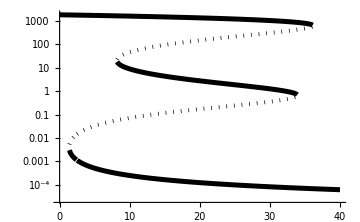

```mathematica
ListLogPlot[(*Join[{Range[0,200,0.1]},*)Transpose[oneDT2](*]*),Joined->True,ImageSize->Medium,DataRange->{0,40},PlotStyle->{{Black,Thickness[0.01]},{Black,Dotted,Thickness[0.008]},{Black,Thickness[0.01]},{Black,Dotted,Thickness[0.008]},{Black,Thickness[0.01]}},(*PlotRange->{{0,200},{0.001,1000}},*)LabelStyle->{14,GrayLevel[0]}]
```

#### x2 bifurcation plot ? (seems not very easy)

```mathematica
polx2=NSolve[Subscript[x, 2]=-((Subscript[k, 2]^2 Subscript[k, 5] (Subscript[k, 2] Subscript[k, 4] Subscript[k, 5]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6]) Subscript[k, 10] Subscript[k, 11]^2 Subscript[k, 14] Subscript[T, 2] Subscript[x, 1]^2 (-Subscript[k, 13]-Subscript[k, 7] Subscript[x, 1]) ((-Subscript[k, 9] Subscript[k, 10] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 3] Subscript[k, 8] Subscript[k, 12] Subscript[k, 13] Subscript[x, 1]+Subscript[k, 3] Subscript[k, 8] Subscript[k, 13] Subscript[k, 14] Subscript[x, 1]+Subscript[k, 3] Subscript[k, 7] Subscript[k, 8] Subscript[k, 14] Subscript[x, 1]^2)/(Subscript[k, 10] Subscript[k, 14] Subscript[k, 15] (Subscript[k, 13]+Subscript[k, 7] Subscript[x, 1]))-((-Subscript[k, 9]-Subscript[k, 3] Subscript[x, 1]) ((-Subscript[k, 4] Subscript[k, 5]-Subscript[k, 5] Subscript[k, 6]-Subscript[k, 1] Subscript[k, 6] Subscript[x, 1])/(Subscript[k, 5] Subscript[k, 15])-((-Subscript[k, 4]-Subscript[k, 6]) (-Subscript[k, 8]/Subscript[k, 15]-(Subscript[k, 8] Subscript[k, 12] Subscript[k, 13])/(Subscript[k, 14] Subscript[k, 15] (Subscript[k, 13]+Subscript[k, 7] Subscript[x, 1]))))/Subscript[k, 10]))/(Subscript[k, 4]+Subscript[k, 6])))/(-Subscript[k, 2] Subscript[k, 5] (-Subscript[k, 9]-Subscript[k, 3] Subscript[x, 1]) (Subscript[k, 10] Subscript[k, 11] Subscript[k, 14] Subscript[x, 1] (-Subscript[k, 13]-Subscript[k, 7] Subscript[x, 1]) (Subscript[k, 2] Subscript[k, 5] (Subscript[k, 2] Subscript[k, 11] Subscript[x, 1]+Subscript[k, 6] Subscript[k, 11] Subscript[x, 1])+Subscript[k, 2] Subscript[k, 6] (Subscript[k, 2] Subscript[k, 11] Subscript[x, 1]+Subscript[k, 1] Subscript[k, 11] Subscript[x, 1]^2))-(-Subscript[k, 4]-Subscript[k, 6]) (Subscript[k, 2]^2 Subscript[k, 5] Subscript[k, 11]^2 Subscript[k, 14] Subscript[x, 1]^2 (-Subscript[k, 13]-Subscript[k, 7] Subscript[x, 1])-Subscript[k, 8] (Subscript[k, 2] Subscript[k, 5] Subscript[k, 11] Subscript[k, 13] Subscript[x, 1] (Subscript[k, 2] Subscript[k, 12]+Subscript[k, 2] Subscript[k, 11] Subscript[x, 1])+Subscript[k, 2] Subscript[k, 5] Subscript[k, 11] Subscript[k, 14] Subscript[x, 1] (Subscript[k, 2] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 11] Subscript[x, 1]))))+(Subscript[k, 2] Subscript[k, 4] Subscript[k, 5]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6]) (-Subscript[k, 3] Subscript[x, 1] (Subscript[k, 2]^2 Subscript[k, 5] Subscript[k, 11]^2 Subscript[k, 14] Subscript[x, 1]^2 (-Subscript[k, 13]-Subscript[k, 7] Subscript[x, 1])-Subscript[k, 8] (Subscript[k, 2] Subscript[k, 5] Subscript[k, 11] Subscript[k, 13] Subscript[x, 1] (Subscript[k, 2] Subscript[k, 12]+Subscript[k, 2] Subscript[k, 11] Subscript[x, 1])+Subscript[k, 2] Subscript[k, 5] Subscript[k, 11] Subscript[k, 14] Subscript[x, 1] (Subscript[k, 2] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 11] Subscript[x, 1])))+Subscript[k, 10] (Subscript[k, 2]^2 Subscript[k, 5] Subscript[k, 11]^2 Subscript[k, 14] Subscript[x, 1]^2 (-Subscript[k, 13]-Subscript[k, 7] Subscript[x, 1])-Subscript[k, 9] (Subscript[k, 2] Subscript[k, 5] Subscript[k, 11] Subscript[k, 13] Subscript[x, 1] (Subscript[k, 2] Subscript[k, 12]+Subscript[k, 2] Subscript[k, 11] Subscript[x, 1])+Subscript[k, 2] Subscript[k, 5] Subscript[k, 11] Subscript[k, 14] Subscript[x, 1] (Subscript[k, 2] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 11] Subscript[x, 1]))))))/.parSet,{Subscript[x, 1]}];
```

```mathematica
polx2
```

-((9.33424×10^9 T_2 (-0.411001-684.529 x_1) x_1^2 ((0.0910256 (-44926.9+150176. x_1+232409. x_1^2))/(0.411001+684.529 x_1)-0.0303213 (-0.0903776-0.290523 x_1) (84.9499 (-39.7522-0.0491332 x_1)+0.0736404 (-47640.9-(2.10531×10^7)/(0.411001+684.529 x_1)))))/(-0.174498 (-0.0903776-0.290523 x_1) (8.49838×10^6 (-0.411001-684.529 x_1) x_1 (775.045 x_1+0.0641532 (1093.73 x_1+837.657 x_1^2))+32.9801 (3.6216×10^6 (-0.411001-684.529 x_1) x_1^2-465.273 (3311.25 x_1 (0.059501+1093.73 x_1)+541.827 x_1 (390.975+1093.73 x_1))))+5.75496 (-0.290523 x_1 (3.6216×10^6 (-0.411001-684.529 x_1) x_1^2-465.273 (3311.25 x_1 (0.059501+1093.73 x_1)+541.827 x_1 (390.975+1093.73 x_1)))+447.853 (3.6216×10^6 (-0.411001-684.529 x_1) x_1^2-0.0903776 (3311.25 x_1 (0.059501+1093.73 x_1)+541.827 x_1 (390.975+1093.73 x_1))))))

```mathematica
t2=Range[0,40,0.1];
```

```mathematica
oneDT2x2=Table[N[polx2/.{Subscript[x, 1]->oneDT2[[i]],Subscript[T, 2]->t2[[i]]}],{i,1,Length[oneDT2]}];
```

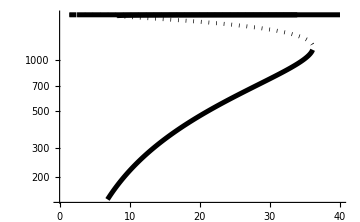

```mathematica
ListLogPlot[(*Join[{Range[0,200,0.1]},*)Transpose[oneDT2x2](*]*),Joined->True,ImageSize->Medium,DataRange->{0,40},PlotStyle->{{Black,Thickness[0.01]},{Black,Dotted,Thickness[0.008]},{Black,Thickness[0.01]},{Black,Dotted,Thickness[0.008]},{Black,Thickness[0.01]}},(*PlotRange->{{0,200},{0.001,1000}},*)LabelStyle->{14,GrayLevel[0]}(*,PlotRange->{{0,40},{0.001,10000}}*)]
```

## Test

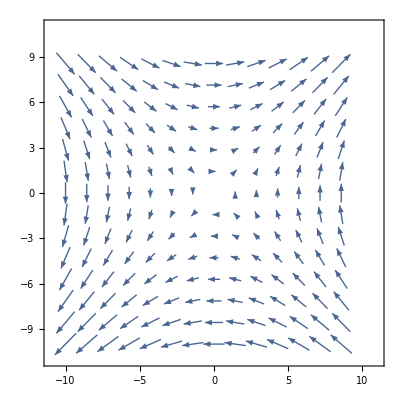

```mathematica
VectorPlot[{y,x},{x,-10,10},{y,-10,10}]
```